# Network Resilience in Power Grids

```mathematica
pgraph=Import["/Users/Kofi/Desktop/Data Science Project/DataDir/power/powergridData.gml"]; (*network graph imported*)
```

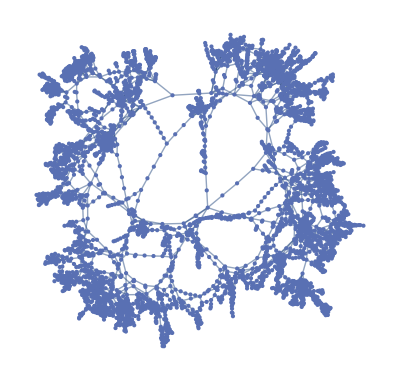

```mathematica
p=SetProperty[pgraph,VertexLabels->Placed["Name",Tooltip]]
```

## Characterisation of the data

```mathematica
VertexCount[p](*Number of vertices*)
```

4941

```mathematica
EdgeCount[p](*Number of edges*)
```

6594

```mathematica
vdpower=VertexDegree[p];(*list of degree of every node*)
```

```mathematica
Max[vdpower](*largest degree*)
```

19

```mathematica
cluscoeff=LocalClusteringCoefficient[p]//N;(*clustering coefficient of every node in the graph*)
```

```mathematica
Max[cluscoeff]
```

1.

### First moment of vertex degrees and a box plot of the degree:

```mathematica
Mean[vdpower]//N
```

2.6691

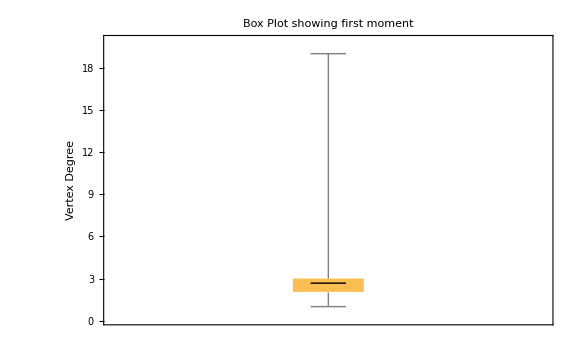

```mathematica
BoxWhiskerChart[vdpower,"Mean",Frame->{True,True,False,False},FrameLabel->{"","Vertex Degree"},PlotRange->All,PlotLabel->"Box Plot showing first moment",ImageSize->Large]
```

Finding the distribution for the vertex degree:

```mathematica
distrVp=FindDistribution[vdpower,3]
```

{MixtureDistribution[{0.815694,0.184306},{BenfordDistribution[5],PoissonDistribution[5.49278]}],MixtureDistribution[{0.944886,0.0551137},{BinomialDistribution[19,0.127617],PoissonDistribution[8.17642]}],MixtureDistribution[{0.883426,0.116574},{BinomialDistribution[19,0.120264],BinomialDistribution[120,0.0516893]}]}

Finding the best fit distribution for the clustering coefficient:

```mathematica
distClCoeff=FindDistribution[cluscoeff]
```

MixtureDistribution[{0.841559,0.158441},{NormalDistribution[0.0194164,0.0656107],NormalDistribution[0.583829,0.371553]}]

Best-fit distribution for the eigenvector centrality:

```mathematica
distEigens = FindDistribution[eigens]
```

MixtureDistribution[{0.941411,0.0585895},{LogNormalDistribution[-25.2453,1.20434],BetaDistribution[0.0800644,15.1314]}]

Best-fit distribution for the betweenness centrality:

```mathematica
distbetweenness = FindDistribution[betweenness]
```

MixtureDistribution[{0.350029,0.649971},{CauchyDistribution[-0.00280911,0.0515932],LogNormalDistribution[9.24237,2.37341]}]

### Histogram plots showing the distribution of the various centrality measures

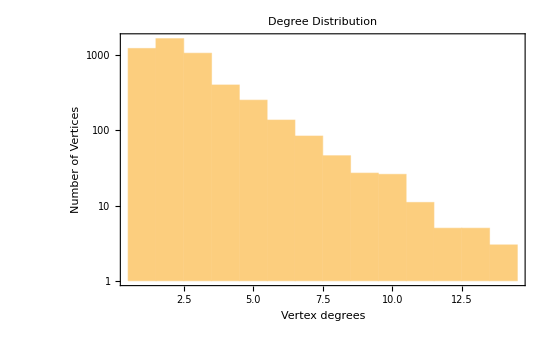

```mathematica
histVertexDegree=Histogram[vdpower,"FreedmanDiaconis",ScalingFunctions->"Log",Frame->{True,True,False,False},PlotLabel->"Degree Distribution",FrameLabel->{"Vertex degrees","Number of Vertices"},AxesLabel->{"Vertex degree",None},PlotRange->{{0,20},{0,1600}}]
```

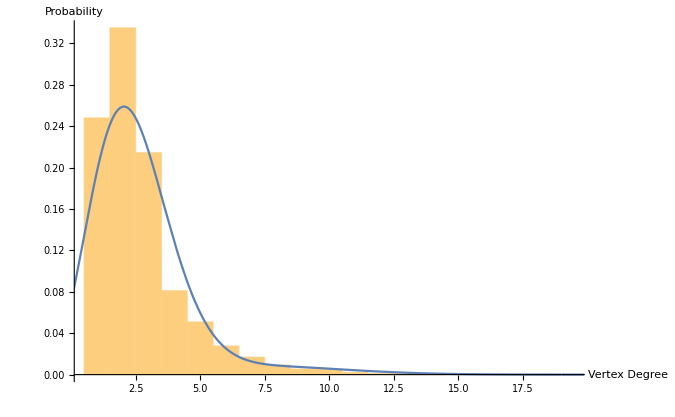

```mathematica
Show[{
Histogram[vdpower,"FreedmanDiaconis","Probability",AxesLabel->{"Vertex Degree","Probability"},PlotRange->All],
Plot[Evaluate@PDF[distrVp[[2]],x],{x,0,20}]
}]
```

```mathematica
histVertexDegree2=Histogram[vdpower,"FreedmanDiaconis",ScalingFunctions->"Log",Frame->{True,True,False,False},PlotLabel->"Degree Distribution",FrameLabel->{"Vertex degrees","Number of Vertices"},AxesLabel->{"Vertex degree",None},PlotRange->{{0,20},{0,1600}}];
histClusCoeff=Histogram[cluscoeff,"FreedmanDiaconis",ScalingFunctions->"Log",AxesLabel->{"Cluster Coefficient","Number of Vertices"},PlotRange->All,PlotLabel->"Clustering Coefficient Distribution"];
histeigens=Histogram[eigens,"Sturges",ScalingFunctions->"Log",PlotLabel->"Eigenvector Centrality Distribution",AxesLabel->{"Eigenvector centrality","Number of Vertices"},PlotRange->All];
histbetweenness=Histogram[betweenness/10^3,"Sturges",ScalingFunctions->"Log",AxesLabel->{"Betweenness centrality (x10^3)","Number of Vertices"},PlotRange->All,PlotLabel->"Betweenness Centrality Distribution"];
```

Grid view of histogram plots on a logarithmic scale in a clockwise direction from the top left, vertex degree, clustering coefficient, eigenvector centrality, and betweenness centrality:

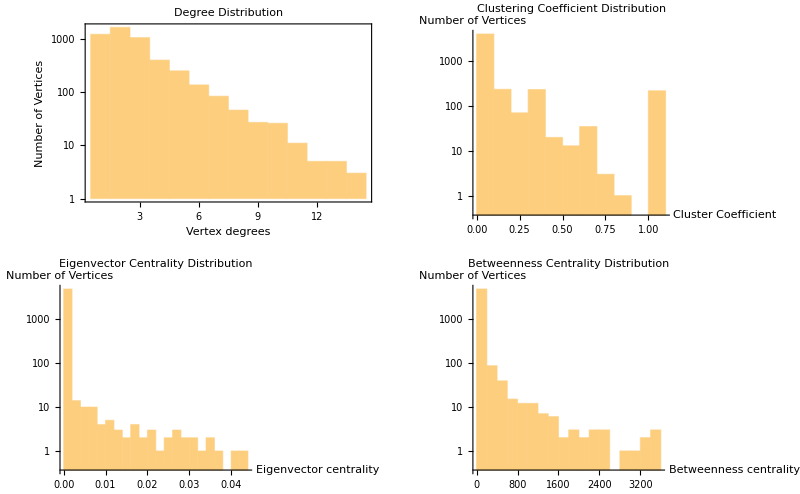

```mathematica
GraphicsGrid[{{histVertexDegree2,histClusCoeff},{histeigens,histbetweenness}},ImageSize->Full]
```

### Identifying hubs and other important nodes based on the centralities, using the quantile

```mathematica
Quantile[vdpower,0.99](*choose vertex degree from list of degrees in the 99% *)
```

10

```mathematica
hubs=Position[vdpower,_?(#>=10&)]-1(*Finding nodes with degrees greater than or equal to 10*)
```

{{490},{725},{831},{1005},{1030},{1050},{1091},{1106},{1166},{1170},{1224},{1309},{1326},{1334},{1460},{2282},{2382},{2434},{2439},{2533},{2542},{2553},{2554},{2575},{2585},{2586},{2608},{2617},{2662},{2717},{2800},{2851},{2936},{3128},{3312},{3355},{3468},{3838},{3895},{4332},{4345},{4346},{4352},{4359},{4361},{4373},{4381},{4384},{4392},{4395},{4402},{4458}}

```mathematica
Length[hubs](*Number of hubs*)
```

52

```mathematica
Quantile[cluscoeff,0.99]
```

1.

```mathematica
Position[cluscoeff,_?(#>=1&)]-1 (*Finding nodes with clustering coefficient greater than or equal to 1*)
```

{{30},{84},{110},{142},{149},{152},{167},{175},{243},{264},{281},{289},{312},{366},{367},{368},{369},{371},{381},{460},{489},{505},{580},{677},{877},{880},{890},{935},{977},{1196},{1322},{1483},{1558},{1617},{1673},{1700},{1775},{1805},{1856},{1857},{1868},{1898},{1918},{2043},{2088},{2135},{2149},{2184},{2232},{2289},{2295},{2299},{2300},{2331},{2333},{2341},{2377},{2403},{2478},{2514},{2520},{2525},{2652},{2678},{2684},{2696},{2706},{2714},{2716},{2719},{2720},{2745},{2756},{2757},{2758},{2774},{2784},{2809},{2811},{2845},{2865},{2866},{2879},{2891},{2903},{2911},{2920},{2935},{2958},{2968},{2969},{2972},{2989},{2995},{2996},{2998},{3018},{3020},{3026},{3028},{3030},{3033},{3034},{3036},{3038},{3042},{3043},{3050},{3055},{3059},{3061},{3063},{3065},{3077},{3079},{3092},{3094},{3095},{3096},{3097},{3098},{3099},{3104},{3109},{3111},{3112},{3113},{3116},{3118},{3119},{3121},{3126},{3130},{3131},{3133},{3134},{3141},{3143},{3144},{3145},{3148},{3149},{3150},{3153},{3157},{3158},{3159},{3161},{3171},{3178},{3179},{3180},{3181},{3190},{3198},{3199},{3200},{3202},{3205},{3207},{3209},{3211},{3213},{3214},{3215},{3221},{3222},{3228},{3230},{3232},{3235},{3238},{3244},{3245},{3246},{3250},{3252},{3253},{3263},{3265},{3267},{3269},{3270},{3275},{3277},{3279},{3399},{3417},{3436},{3558},{3632},{3633},{3725},{3747},{3748},{3805},{3837},{3860},{3865},{3867},{3876},{3884},{3920},{3921},{3928},{3931},{3935},{3953},{4018},{4064},{4136},{4150},{4159},{4337},{4354},{4400},{4405},{4406},{4411},{4419},{4799}}

```mathematica
eigens=EigenvectorCentrality[p];
```

```mathematica
Quantile[eigens,0.99]
```

0.00585253

```mathematica
Position[eigens,_?(#>=.00585&)]-1 (*Finding nodes with eigenvector centrality greater than or equal to 0.00585*)
```

{{4327},{4332},{4333},{4335},{4336},{4340},{4342},{4343},{4344},{4345},{4346},{4347},{4352},{4357},{4359},{4361},{4363},{4364},{4365},{4367},{4368},{4369},{4370},{4371},{4372},{4373},{4374},{4375},{4376},{4381},{4383},{4384},{4385},{4386},{4391},{4392},{4395},{4396},{4398},{4400},{4401},{4402},{4404},{4405},{4406},{4408},{4409},{4413},{4418},{4419}}

```mathematica
betweenness = BetweennessCentrality[p];
```

```mathematica
Quantile[betweenness,0.99]
```

923264.

```mathematica
Position[betweenness,_?(#>=923263.6428569602&)]-1 (*Finding nodes with degrees greater than or equal to 10*)
```

{{69},{70},{108},{285},{393},{396},{420},{426},{427},{1091},{1125},{1131},{1148},{1166},{1167},{1178},{1243},{1244},{1267},{1308},{1340},{1476},{2223},{2231},{2235},{2249},{2298},{2312},{2317},{2343},{2370},{2528},{2532},{2543},{2557},{2594},{2605},{2606},{2612},{3785},{4120},{4164},{4199},{4206},{4207},{4219},{4476},{4652},{4832},{4837}}

## Node Removal modelling strategies for network resilience

#### Random Attacks/Failures

```mathematica
p=Graph[p];
```

```mathematica
ran100=Module[{gSec,netwk,r,gtemp,randomAttack},

gSec = p; (*creating a security variable to keep the initial input graph for the the loop*)
netwk=gSec;
size0 = VertexCount[netwk];
randomAttack = Table[
r=Flatten@RandomSample[VertexList[netwk],1];(*select one node randomly from the sample of vertices in the graph*)
gtemp =VertexDelete[netwk,r];(*creates a new graph after deleting the node r from the graph*)
sizeGiantC = Max[Length/@ConnectedComponents[gtemp]];(*calculate the largest connected component of the new graph*)
netwk=gtemp;(*swap graph for next iteration*)
{i,sizeGiantC},{i,1,size0-1}(*creates paired list of giant component the size of the graph from the initial grpah till the graph completely disintegrates*)
]
]
```

{{1,4939},{2,4938},{3,4937},{4,4935},{5,4934},{6,4933},{7,4931},{8,4930},{9,4925},{10,4923},{11,4922},{12,4921},{13,4920},{14,4919},{15,4918},{16,4917},{17,4916},{18,4915},{19,4914},{20,4913},{21,4912},{22,4911},{23,4909},{24,4907},{25,4906},{26,4905},{27,4904},{28,4903},4884,{4913,1},{4914,1},{4915,1},{4916,1},{4917,1},{4918,1},{4919,1},{4920,1},{4921,1},{4922,1},{4923,1},{4924,1},{4925,1},{4926,1},{4927,1},{4928,1},{4929,1},{4930,1},{4931,1},{4932,1},{4933,1},{4934,1},{4935,1},{4936,1},{4937,1},{4938,1},{4939,1},{4940,1}}
 |  |  |  |

Plot showing model of random attack of nodes in one event. It shows the decrease in the size of the giant component against the fraction of nodes removed:

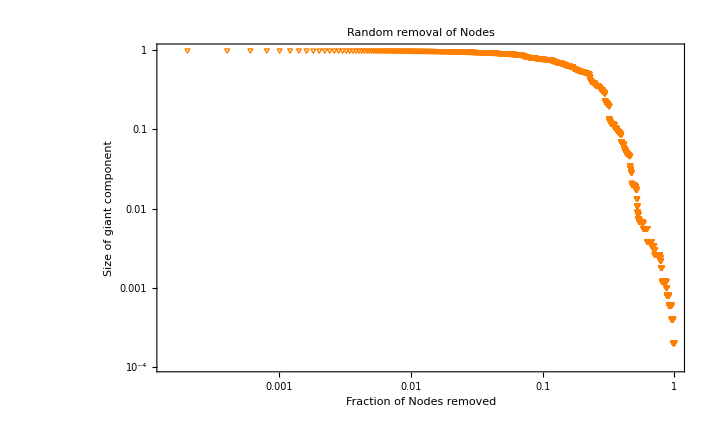

```mathematica
ListLogLogPlot[ran100/Length@ran100,PlotMarkers->▽,PlotStyle->Orange,Frame->{True,True,False,False},FrameLabel->{"Fraction of Nodes removed","Size of giant component"},PlotLabel->"Random removal of Nodes"]
```

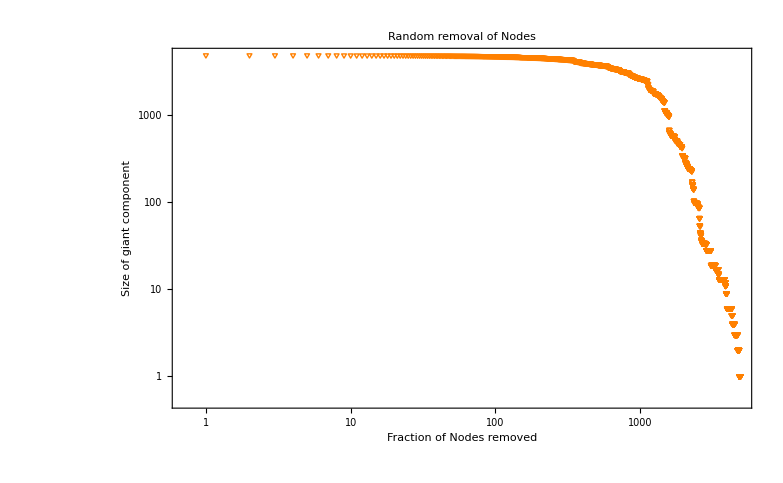

```mathematica
ListLogLogPlot[ran100,PlotMarkers->▽,PlotStyle->Orange,Frame->{True,True,False,False},FrameLabel->{"Fraction of Nodes removed","Size of giant component"},PlotLabel->"Random removal of Nodes"]
```

In the plot above, the model shows how the size of the giant component reduces (an indicator of how quickly the network disintegrates) under a uniform random removal of nodes. The giant connected component gradually decreases to about 50% of the initial size. There is a sudden jump to 35% of the original giant component after removing about 30% of the nodes from the network. The size decreases significantly from 25% of the original giant component to 15% of the original giant component after removing 30% of the nodes in the network. Afterwards, the giant component decreases further until there is no more a giant component after removing about 55% of the nodes.

Creating random attacks/failures 10 (n) times:

```mathematica
ranNtimes=Module[{gSec,netwk,r,gtemp,randomAttack},
Table[
gSec = p;
netwk=gSec;
size0 = VertexCount[netwk];
randomAttack = Table[
r=Flatten@RandomSample[VertexList[netwk],1];
gtemp =VertexDelete[netwk,r];
sizeGiantC = Max[Length/@ConnectedComponents[gtemp]];
netwk=gtemp;
{i,sizeGiantC},{i,1,size0-1}
],
{j,1,10}(*Create 10 different random attacks*)
]
]
```

$Aborted

Plot showing model of random attack of nodes in 10 events:

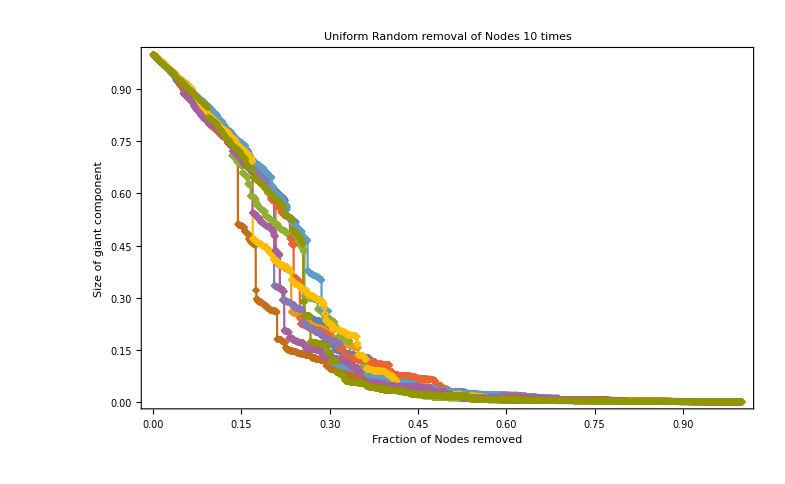

```mathematica
ListLinePlot[ranNtimes/Length@ranNtimes[[2]],PlotMarkers->◇,Frame->{True,True,False,False},FrameLabel->{"Fraction of Nodes removed","Size of giant component"},PlotLabel->"Uniform Random removal of Nodes 10 times"]
```

#### Targeted attack using the centrality measures

Removing nodes according to the largest node degree

```mathematica
g=Graph[p];(*set graph for input*)
```

```mathematica
ndegreeFail=Module[{gnet,del,netTemp,sizeGiantComp,targetDegreeAttack},
gnet=g;
g=gnet;
sizeZero = VertexCount[g];
targetDegreeAttack = Table[
del=First[Pick[VertexList[g],VertexDegree[g],Max[VertexDegree[g]]]];(*Selecting the node with the largest degree. First is used to pick one node at a time in the case where there are more than one node with the largest degree*)
netTemp=VertexDelete[g,del];(*Create new graph from deleting the selected node from the previous graph*)
sizeGiantComp=Max[Length/@ConnectedComponents[netTemp]];(*Calculate size of giant component*)
g=netTemp;(*swap new graph to be set as input for the next iteration*)
{i, sizeGiantComp},{i,1,(sizeZero-1)}

]
]
```

{{1,4939},{2,4927},{3,4917},{4,4902},{5,4901},{6,4897},{7,4895},{8,4890},{9,4889},{10,4880},{11,4869},{12,4866},{13,4861},{14,4858},{15,4854},{16,4851},{17,4848},{18,4831},{19,4827},{20,4826},{21,4825},{22,4807},{23,4796},{24,4791},{25,4790},{26,4789},{27,4787},{28,4774},4884,{4913,1},{4914,1},{4915,1},{4916,1},{4917,1},{4918,1},{4919,1},{4920,1},{4921,1},{4922,1},{4923,1},{4924,1},{4925,1},{4926,1},{4927,1},{4928,1},{4929,1},{4930,1},{4931,1},{4932,1},{4933,1},{4934,1},{4935,1},{4936,1},{4937,1},{4938,1},{4939,1},{4940,1}}
 |  |  |  |

Plot showing model attacks by largest node degree:

```mathematica
ListPlot[ndegreeFail/Length@ndegreeFail,PlotMarkers->"x",Frame->{True,True,False,False},FrameLabel->{"Fraction of nodes removed","Size of giant component"},PlotRange->All,PlotStyle->Red,ImageSize->Large,PlotLabel->"Node removal by highest vertex degree"]
```

-Graphics-

```mathematica
ListLogLogPlot[ndegreeFail,PlotMarkers->"x",Frame->{True,True,False,False},FrameLabel->{"Number of nodes removed","Size of giant component"},PlotRange->All,PlotStyle->Red,ImageSize->Large,PlotLabel->"Node removal by highest vertex degree"]
```

-Graphics-

Removing nodes by the largest clustering coefficient:

```mathematica
netwk=Graph[p];
```

```mathematica
clusteringFail=Module[{gnet,del,netTemp,sizeGiantComp,targetClusterAttack},
gnet=netwk;
netwk=gnet;
sizeZero3= VertexCount[netwk];
targetClusterAttack = Table[
del=First[Pick[VertexList[netwk],LocalClusteringCoefficient[netwk],Max[LocalClusteringCoefficient[netwk]]]];(*Select node with largest clustering coefficient to be removed*)
netTemp=VertexDelete[netwk,del];(*remove node from graph. creates new graph*)
sizeGiantComp=Max[Length/@ConnectedComponents[netTemp]];(*calculate largest component*)
netwk=netTemp;(*swap new graph for next node removal*)
{i,sizeGiantComp},{i,1,sizeZero3-1}

]
]
```

{{1,4940},{2,4939},{3,4938},{4,4937},{5,4936},{6,4935},{7,4934},{8,4933},{9,4932},{10,4931},{11,4930},{12,4929},{13,4928},{14,4927},{15,4926},{16,4925},{17,4924},{18,4923},{19,4922},{20,4921},{21,4920},{22,4919},{23,4918},{24,4917},{25,4916},{26,4915},{27,4914},{28,4913},4884,{4913,9},{4914,9},{4915,9},{4916,9},{4917,9},{4918,9},{4919,9},{4920,9},{4921,9},{4922,9},{4923,9},{4924,9},{4925,9},{4926,9},{4927,9},{4928,9},{4929,9},{4930,9},{4931,7},{4932,7},{4933,4},{4934,2},{4935,2},{4936,2},{4937,2},{4938,2},{4939,2},{4940,1}}
 |  |  |  |

Plot showing model of attack by clustering coefficient metric:

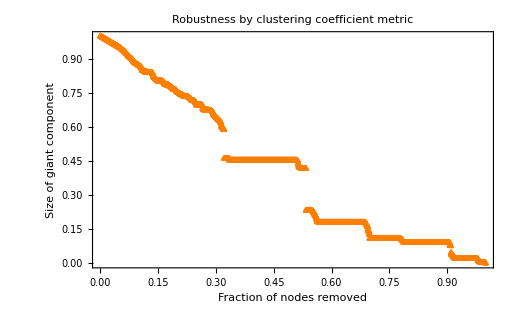

```mathematica
ListPlot[clusteringFail/Length@clusteringFail,PlotRange->Automatic,Frame->{True,True,False,False},FrameLabel->{"Fraction of nodes removed","Size of giant component"},PlotMarkers->△,PlotStyle->Orange,PlotLabel->"Robustness by clustering coefficient metric"]
```

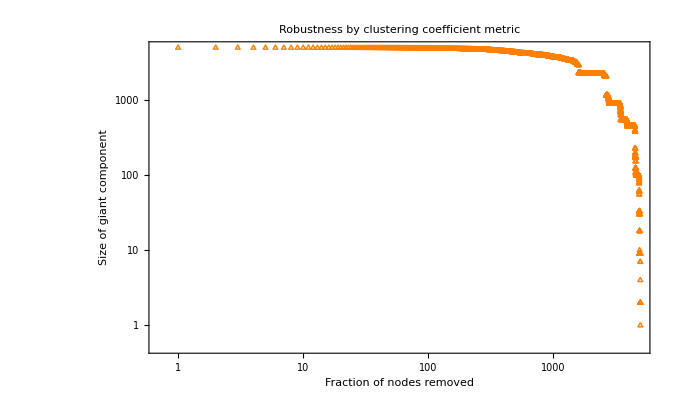

```mathematica
ListLogLogPlot[clusteringFail,PlotRange->Automatic,Frame->{True,True,False,False},FrameLabel->{"Fraction of nodes removed","Size of giant component"},PlotMarkers->△,PlotStyle->Orange,PlotLabel->"Robustness by clustering coefficient metric"]
```

Removing nodes sequentially by the largest eigenvector centrality:

```mathematica
g2=Graph[p];(*graph for input*)
```

```mathematica
eigenvectorFail=Module[{gnet,del,netTemp,sizeGiantComp,targeteigenAttack},
gnet=g2;
g2=gnet;
size4= VertexCount[g2];
targeteigenAttack=Table[
size4= VertexCount[g2];
del=First[Pick[VertexList[g2],EigenvectorCentrality[g2],Max[EigenvectorCentrality[g2]]]];(*Selecting node with largest eigenvector centrality to remove*)
netTemp=VertexDelete[g2,del];(*remove selected node which leaves the rest of the graph*)
sizeGiantComp=Max[Length/@ConnectedComponents[netTemp]];(*calculate size of the giant component *)
g2=netTemp;(*swap new graph for next node removal*)
{i,sizeGiantComp},{i,1,size4-1}

]
]
```

{{1,4940},{2,4939},{3,4938},{4,4936},{5,4935},{6,4933},{7,4931},{8,4929},{9,4928},{10,4926},{11,4925},{12,4924},{13,4923},{14,4922},{15,4917},{16,4916},{17,4915},{18,4913},{19,4912},{20,4911},{21,4910},{22,4898},{23,4883},{24,4872},{25,4871},{26,4870},{27,4854},{28,4852},4884,{4913,1},{4914,1},{4915,1},{4916,1},{4917,1},{4918,1},{4919,1},{4920,1},{4921,1},{4922,1},{4923,1},{4924,1},{4925,1},{4926,1},{4927,1},{4928,1},{4929,1},{4930,1},{4931,1},{4932,1},{4933,1},{4934,1},{4935,1},{4936,1},{4937,1},{4938,1},{4939,1},{4940,1}}
 |  |  |  |

Plot showing model of attack by eigenvector centrality metric:

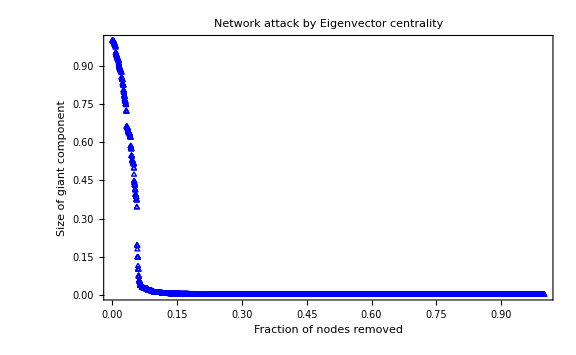

```mathematica
ListPlot[eigenvectorFail/Length@eigenvectorFail,PlotMarkers->△,PlotRange->Full,PlotStyle->Blue,ImageSize->Large,Frame->{True,True,False,False},FrameLabel->{"Fraction of nodes removed","Size of giant component"},PlotLabel->"Network attack by Eigenvector centrality"]
```

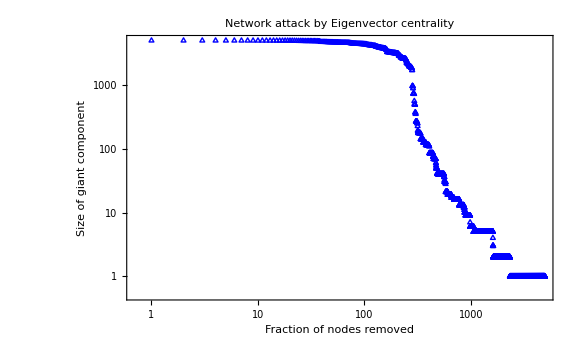

```mathematica
ListLogLogPlot[eigenvectorFail,PlotMarkers->△,PlotRange->Full,PlotStyle->Blue,ImageSize->Large,Frame->{True,True,False,False},FrameLabel->{"Fraction of nodes removed","Size of giant component"},PlotLabel->"Network attack by Eigenvector centrality"]
```

Removing nodes by the largest betweenness centrality

```mathematica
g3=Graph[p];
```

```mathematica
betweennessFail=Module[{gnet,del,netTemp,sizeGiantComp,betweenAttack},
gnet=g3;
g3=gnet;
size5= VertexCount[g3];
betweenAttack = Table[
del=First[Pick[VertexList[g3],BetweennessCentrality[g3],Max[BetweennessCentrality[g3]]]];(*Selecting node with largest betweenness centrality to remove*)
netTemp=VertexDelete[g3,del];(**remove selected node*)
sizeGiantComp=Max[Length/@ConnectedComponents[netTemp]];(*calculate size of giant component*)
g3=netTemp;(*swap new graph for next node removal*)
{i,sizeGiantComp},{i,1,size5-1}

]
]
```

{{1,4940},{2,4939},{3,4938},{4,4937},{5,4936},{6,4935},{7,4933},{8,4930},{9,4929},{10,4927},{11,4924},{12,4923},{13,4922},{14,4921},{15,4918},{16,4917},{17,4915},{18,3888},{19,3887},{20,3882},{21,3880},{22,3878},{23,3877},{24,3874},{25,3873},{26,3872},{27,3868},{28,2481},4884,{4913,2},{4914,2},{4915,2},{4916,2},{4917,2},{4918,2},{4919,2},{4920,2},{4921,2},{4922,2},{4923,2},{4924,2},{4925,2},{4926,2},{4927,2},{4928,2},{4929,2},{4930,2},{4931,2},{4932,2},{4933,2},{4934,2},{4935,2},{4936,2},{4937,2},{4938,1},{4939,1},{4940,1}}
 |  |  |  |

Plot showing model of attack by betweenness centrality metric:

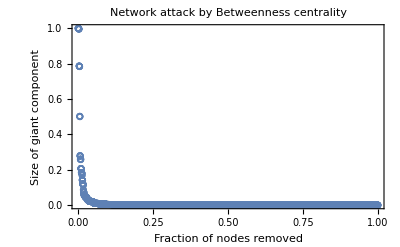

```mathematica
ListPlot[betweennessFail/Length@betweennessFail,PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Fraction of nodes removed","Size of giant component"},PlotMarkers->◦,PlotLabel->"Network attack by Betweenness centrality"]
```

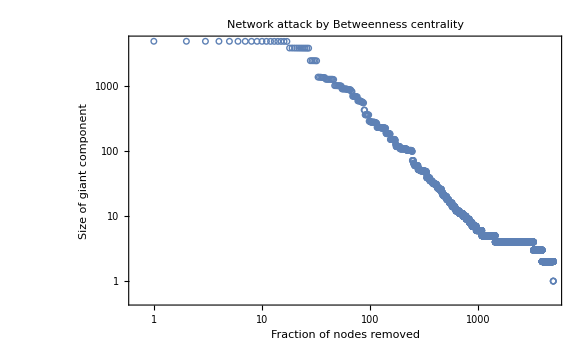

```mathematica
ListLogLogPlot[betweennessFail,PlotRange->All,Frame->{True,True,False,False},FrameLabel->{"Fraction of nodes removed","Size of giant component"},PlotMarkers->◦,PlotLabel->"Network attack by Betweenness centrality"]
```

Comparing the model attacks in the targeted node removal strategy:

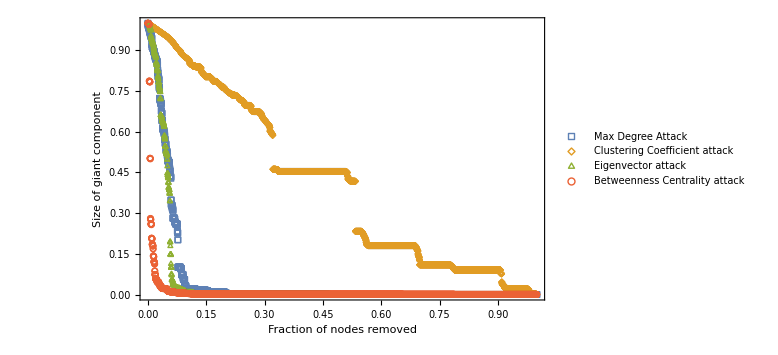

```mathematica
ListPlot[{ndegreeFail/Length@ndegreeFail,clusteringFail/Length@clusteringFail,eigenvectorFail/Length@eigenvectorFail,betweennessFail/Length@betweennessFail},PlotLegends->{"Max Degree Attack",
"Clustering Coefficient attack","Eigenvector attack","Betweenness Centrality attack"},ImageSize->Large,PlotMarkers->{□,◇,△,○},Frame->{True,True,False,False},FrameLabel->{"Fraction of nodes removed","Size of giant component"},PlotRange->All]
```

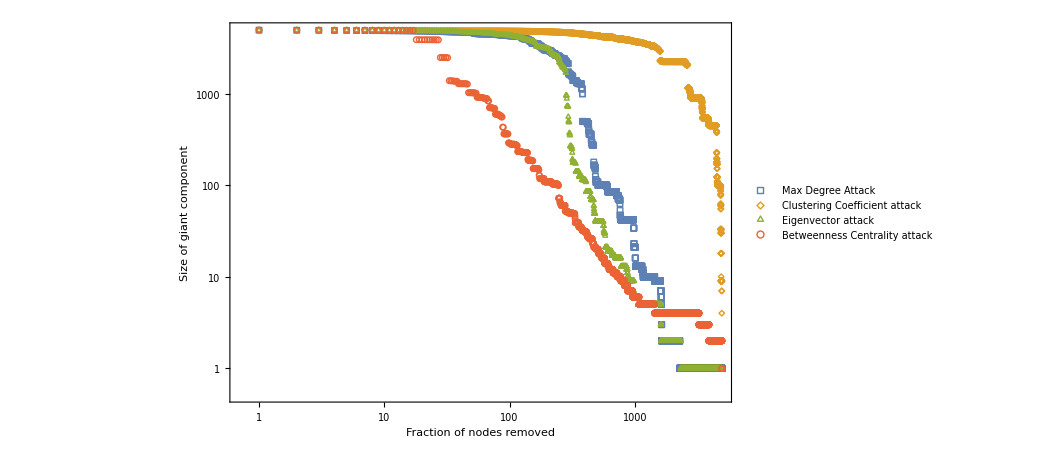

```mathematica
ListLogLogPlot[{ndegreeFail,clusteringFail,eigenvectorFail,betweennessFail},PlotLegends->{"Max Degree Attack",
"Clustering Coefficient attack","Eigenvector attack","Betweenness Centrality attack"},ImageSize->Large,PlotMarkers->{□,◇,△,○},Frame->{True,True,False,False},FrameLabel->{"Fraction of nodes removed","Size of giant component"},PlotRange->All]
```

From the graph plotted above, the evidence shows that the network is most less resilient to attacks under a betweenness centrality removal metric. We see a near vertical decrease in the size of the giant component; the giant component drops to 80% of the initial on removal on less than 5% of the nodes, a further drop to about 50% of the initial giant component on removal of still less than 5% of the nodes and then the network fragments to a point where there is no connectedness (i.e size of giant component 0) after removal of about 10% of the nodes. In a similar fashion, node removal by node degree and eigenvector centrality show a similar decrease in the size of the giant component. The node removal by clustering coefficient seems to be relatively less vulnerable with intermittent big drops in the giant component at 30% and 55% of nodes removed; the network collapses after removing about 85% of the nodes.